```mathematica
(*Assignment 4*)
```

```mathematica
Remove["Global`*"]
```

```mathematica
(* 1. Forced Oscillator *)
```

```mathematica
soln=DSolve[{x''[t]+2*β*x'[t]+Subscript[ω, 0]^2*x[t]==A*Cos [2 Pi/τ*t],x[0]==0,x'[0]==0},x[t],t]/.{Subscript[ω, 0]->2*Pi}
```

{{x[t]→(-4 A ⅇ^(t (-β-√(-4 π^2+β^2))) π^2 β τ^2+4 A ⅇ^(t (-β+√(-4 π^2+β^2))) π^2 β τ^2-4 A ⅇ^(t (-β-√(-4 π^2+β^2))) π^2 √(-4 π^2+β^2) τ^2-4 A ⅇ^(t (-β+√(-4 π^2+β^2))) π^2 √(-4 π^2+β^2) τ^2-4 A ⅇ^(t (-β-√(-4 π^2+β^2))) π^2 β τ^4+4 A ⅇ^(t (-β+√(-4 π^2+β^2))) π^2 β τ^4+4 A ⅇ^(t (-β-√(-4 π^2+β^2))) π^2 √(-4 π^2+β^2) τ^4+4 A ⅇ^(t (-β+√(-4 π^2+β^2))) π^2 √(-4 π^2+β^2) τ^4+8 A π^2 √(-4 π^2+β^2) τ^2 Cos[(2 π t)/τ]-8 A π^2 √(-4 π^2+β^2) τ^4 Cos[(2 π t)/τ]-8 A π β √(-4 π^2+β^2) τ^3 Sin[(2 π t)/τ])/(2 √(-4 π^2+β^2) (-4 π^2+4 π^2 τ^2-2 β^2 τ^2+2 β √(-4 π^2+β^2) τ^2) (4 π^2-4 π^2 τ^2+2 β^2 τ^2+2 β √(-4 π^2+β^2) τ^2))}}

```mathematica
FullSimplify[soln[[1]]]
```

{x[t]→(A ⅇ^(-t (β+√(-4 π^2+β^2))) τ^2 (π (-(1+ⅇ^(2 t √(-4 π^2+β^2))) √(-4 π^2+β^2) (-1+τ^2)-(-1+ⅇ^(2 t √(-4 π^2+β^2))) β (1+τ^2))+2 ⅇ^(t (β+√(-4 π^2+β^2))) √(-4 π^2+β^2) (π (-1+τ^2) Cos[(2 π t)/τ]+β τ Sin[(2 π t)/τ])))/(8 π √(-4 π^2+β^2) (β^2 τ^2+π^2 (-1+τ^2)^2))}

```mathematica
(*this is the solution to the forced oscillator differential equation with the given intial conditions*)
```

```mathematica
X[t_]=x[t]/.soln[[1]]
```

(-4 A ⅇ^(t (-β-√(-4 π^2+β^2))) π^2 β τ^2+4 A ⅇ^(t (-β+√(-4 π^2+β^2))) π^2 β τ^2-4 A ⅇ^(t (-β-√(-4 π^2+β^2))) π^2 √(-4 π^2+β^2) τ^2-4 A ⅇ^(t (-β+√(-4 π^2+β^2))) π^2 √(-4 π^2+β^2) τ^2-4 A ⅇ^(t (-β-√(-4 π^2+β^2))) π^2 β τ^4+4 A ⅇ^(t (-β+√(-4 π^2+β^2))) π^2 β τ^4+4 A ⅇ^(t (-β-√(-4 π^2+β^2))) π^2 √(-4 π^2+β^2) τ^4+4 A ⅇ^(t (-β+√(-4 π^2+β^2))) π^2 √(-4 π^2+β^2) τ^4+8 A π^2 √(-4 π^2+β^2) τ^2 Cos[(2 π t)/τ]-8 A π^2 √(-4 π^2+β^2) τ^4 Cos[(2 π t)/τ]-8 A π β √(-4 π^2+β^2) τ^3 Sin[(2 π t)/τ])/(2 √(-4 π^2+β^2) (-4 π^2+4 π^2 τ^2-2 β^2 τ^2+2 β √(-4 π^2+β^2) τ^2) (4 π^2-4 π^2 τ^2+2 β^2 τ^2+2 β √(-4 π^2+β^2) τ^2))

```mathematica
(* 1. a. *)
```

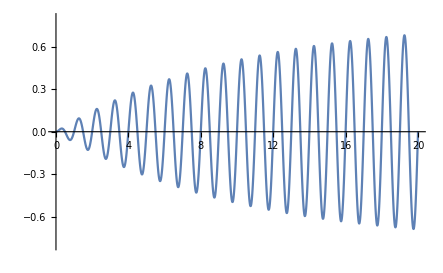

```mathematica
Plot[X[t]/.{A->1,τ->1,β->0.1},{t,0,20},PlotRange->{{0,20},{-.8,.8}}]
```

```mathematica
(*this plot is for the resonance condition when ω=Subscript[ω, 0]*)
```

```mathematica
(* 1. b. *)
```

```mathematica
Manipulate[Plot[X[t]/.{A->1,τ->1,β->damp},{t,0,20},PlotRange->{{0,20},{-.8,.8}}],{damp,0.1,10}]
```

```mathematica
(*if there were no driving force to sustain oscillations, then for β>Subscript[ω, 0] there would be no oscillations, i.e. for β>2π*)
```

```mathematica
(* 1. c. *)
```

```mathematica
Manipulate[Plot[X[t]/.{A->1,τ->ftime,β->0.1},{t,0,20}],{ftime,0.1,5}]
```

```mathematica
(*value of τ at resonance = 1 *)
```

```mathematica
(* 1. d. *)
```

```mathematica
Manipulate[Module[{y=NDSolve[{v[t]==x'[t],
v'[t]+2*β*v[t]+Subscript[ω, 0]^2 *x[t]==A*Cos[ω*t],
x[0]==p[[1]],v[0]==p[[2]]},{x[t],v[t]},{t,0,time}]},ParametricPlot[Evaluate[{x[t],v[t]}/.y],{t,0,time},PlotRange->{{-7,7},{-7,7}}]],{{p,{0,0}},Locator},
{{time,10},0,100},{ω,Pi/4,4Pi},{A,0.5,5},{Subscript[ω, 0],Pi,3Pi},{β,0.1,2}]
```

```mathematica
(*at resonance, the phase space orbit eventually spirals from its initial position into an ellipse like that of an undamped regualar harmonic oscillator. the x intercept is the resonant amplitude*)
(*for Subscript[ω, 0]/ω being a rational no. other than 1, then for a particular intiial condition it comes out to be an ellipse. for other values it is a somewhat haphazard plot*)
```

```mathematica
(* 2. Humped Potential Well *)
```

```mathematica
soln2=Evaluate@Table[{NDSolve[{m*x''[t]==a*(x[t])^2-b*x[t],x[0]==Subscript[s, 0],x'[0]==0},x[t],{t,0,30}]},{Subscript[s, 0],{-0.9999 b/(2a),-.0001 b/(2a),.0001 b/(2a),.9999 b/(2a)}}]/.{m->1,a->1,b->4}
```

{{{{x[t]→InterpolatingFunction[{{0., 30.}}, <>][t]}}},{{{x[t]→InterpolatingFunction[{{0., 30.}}, <>][t]}}},{{{x[t]→InterpolatingFunction[{{0., 30.}}, <>][t]}}},{{{x[t]→InterpolatingFunction[{{0., 30.}}, <>][t]}}}}

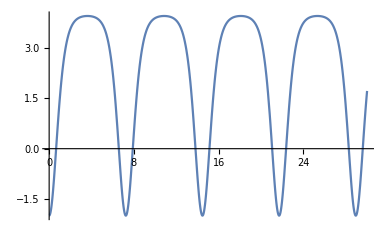
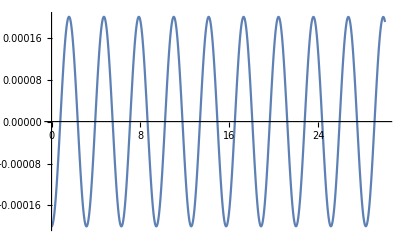
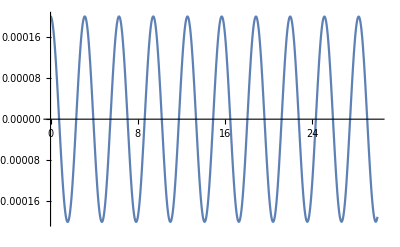
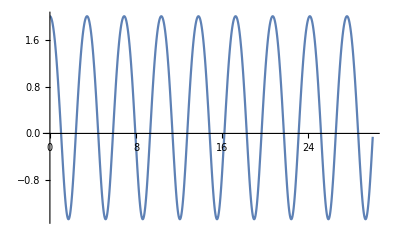

```mathematica
Table[Plot[x[t]/.soln2[[n]],{t,0,30},PlotRange->Full],{n,1,4}]
```

```mathematica
(*first plot is for x close to -b/2a, second and third for |x|<< b/2a and last for x close to b/2a*)
(*close to 0, the potential curve can be approximated as a parabola and the motion is nearly SHM*)
(*for x=-b/2a, the time perod goes to ∞ as the potential at (-b/2a) is equal to the potential at b/a which is an equilibrium point. thus the particle will stop after reaching b/a*)
```

```mathematica
U[x_]=-∫_0^x (a*u^2-b*u)ⅆu
```

(b x^2)/2-(a x^3)/3

```mathematica
U[b/2a]/.{a->1,b->4}
```

16/3

```mathematica
(*b/2a is an inflection point*)
```

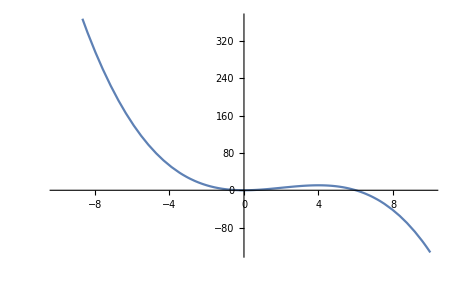

```mathematica
Plot[U[x]/.{a->1,b->4},{x,-10,10}]
```

```mathematica
V[x_]:=-a x^2/2+b x^4/4
```

```mathematica
Manipulate[Plot[V[x]/.{a->α,b->β},{x,-10,10}],{α,-3,3},{β,.1,1}]
```

```mathematica
(*when a<0, only a single well exists, the double well is formed when a crosses 0*)
```

```mathematica
Manipulate[Module[{y=NDSolve[{x'[t]==v[t],
m*v'[t]==-V'[x[t]]/.{a->α,b->β},
x[0]==p[[1]],v[0]==p[[2]]},{x[t],v[t]},{t,0,time}]/.m->1},
ParametricPlot[Evaluate[{x[t],v[t]}/.y],{t,0,time},PlotRange->{{-10,10},{-10,10}}]],{{p,{2,4}},Locator},
{{time,20},0.,50},{α,0,10},{β,0.1,1}]
```

```mathematica
(*here the separatrix is at E=0. if the total energy of the system is greater than 0 the orbits will traverse both potential wells and if they are less than 0 they will be bound to a single potential well*)
```

```mathematica
Manipulate[Module[{y=NDSolve[{x'[t]==v[t],
m*v'[t]==-V'[x[t]]-k*v[t]/.{a->α,b->β},
x[0]==p[[1]],v[0]==p[[2]]},{x[t],v[t]},{t,0,time}]/.m->1},
ParametricPlot[Evaluate[{x[t],v[t]}/.y],{t,0,time},PlotRange->{{-15,15},{-15,15}}]],{{p,{2,2}},Locator},
{{time,20},0,50},{α,0,10},{β,0.1,1},{k,0,1}]
```

```mathematica
(*by varying the intial conditions through the locator in the plot, we can see that whenever a part of the orbit approaches the origin (or approaches the separatrix lines) the well into which the particle falls is switched*)
```

```mathematica
Manipulate[Module[{y=NDSolve[{x'[t]==v[t],
m*v'[t]==-V'[x[t]]-k*v[t]+A Cos[ω t]/.{a->α,b->β},
x[0]==p[[1]],v[0]==p[[2]]},{x[t],v[t]},{t,0,time}]/.m->1},
ParametricPlot[Evaluate[{x[t],v[t]}/.y],{t,0,time},PlotRange->{{-10,10},{-10,10}}]],{{p,{2,3}},Locator},
{{time,25},0.01,50},{{α,3},0,10},{{β,0.3},0.1,1},{{ω,Pi},0,3Pi},{{k,0.3},0,1},{A,0,3}]
```

```mathematica
(* by adding forcing we can achieve sustained oscillations (elliptical phase space plot) (when x'[0]=0 and x[0] is some Subscript[x, 0])but only for very specific initial conditions(when x'[0]=0 and x[0] is some Subscript[x, 0]). otherwise the orbit is disordered*)
```